```mathematica
s0={"[[0,3],[0,5],[0,6],[1,4],[1,5],[1,6],[2,4],[2,5],[2,6],[3,5],[3,6],[4,6]]",
"[000000000010,1]",
"[000000000011,1]",
"[000000000100,1]",
"[000000000101,1]",
"[000000000110,2]",
"[000000000111,2]",
"[000000001010,2]",
"[000000001100,4]",
"[000000001110,4]",
"[000000010010,5]",
"[000000101101,5]",
"[000001001100,7]",
"[000001010010,8]",
"[000001010110,8]",
"[000001100101,9]",
"[000001101101,9]",
"[000010010010,9]",
"[000010110010,9]",
"[000011110010,9]",
"[000100001101,9]",
"[000101001101,9]",
"[000101101101,9]",
"[000110010010,9]",
"[000110011010,9]",
"[001001010010,11]",
"[001010001010,11]",
"[001010010010,16]",
"[001010110010,16]",
"[001110010010,16]",
"[010001101101,16]",
"[010101001101,16]",
"[010101101101,16]"};
```

```mathematica
parsep[string_]:=
Block[{prestring = StringSplit[StringReplace[string,{"["->"","]"->""}],","]},
{Map[ToExpression,Characters[prestring[[1]]]],ToExpression[prestring[[2]]]}]
```

```mathematica
check[string_]:=Block[{graphlist =ToExpression[StringReplace[string[[1]],{"["->"{","]"->"}"}]], dlists=Map[parsep,string[[2;;]]]},Map[checkone[graphlist,#]&,dlists]]
check[s0]
```

{{0,1},{0,1},{0,1},{0,1},{0,2},{0,2},{1,2},{2,4},{1,4},{2,5},{2,5},{4,7},{5,8},{3,8},{5,9},{4,9},{4,9},{4,9},{5,9},{5,9},{4,9},{4,9},{4,9},{5,9},{9,11},{9,11},{12,16},{12,16},{12,16},{12,16},{12,16},{12,16}}

```mathematica
comb[graphlist_,dlist_]:=Table[Piecewise[{{graphlist[[i]], dlist[[i]]==0}, {Reverse[graphlist[[i]]], dlist[[i]]==1}}],{i,1,Length[dlist]}]
checkone[graphlist_,otherlist_]:={Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,comb[graphlist,otherlist[[1]]]]],∞,All]],otherlist[[2]]}
```

```mathematica
{1,2,3,4,5}[[2;;]]
```

{2,3,4,5}

```mathematica
dlists0=Table[{PadLeft[IntegerDigits[j,2],12],0},{j,0,2^12-1}];
Map[First,Block[{graphlist =ToExpression[StringReplace[s0[[1]],{"["->"{","]"->"}"}]], dlists=dlists0},Map[checkone[graphlist,#]&,dlists]]]
```

```mathematica
Max[%]
```

12

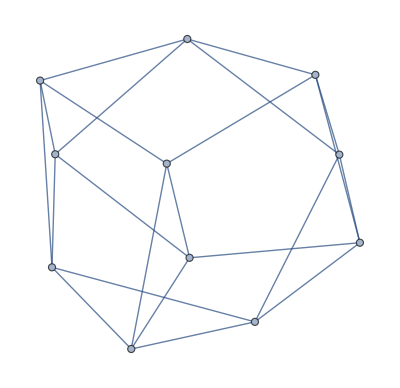
```mathematica
Map[{#[[1]],#[[2]]}&,EdgeList[-Graphics-]]
```

```mathematica
g2l={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,6},{3,5},{3,7},{4,8},{4,9},{5,10},{5,11},{6,7},{6,8},{6,10},{7,8},{7,11},{8,9},{9,10},{9,11},{10,11}};
           [[0,1],[0,2],[0,3],[0,4],[1,2],[1,3],[1,5],[2,4],[2,6],[3,7],[3,8],[4,9],   [4,10],[5,6],[5,7],[5,9],  [6,7],[6,10],[7,8],[8,9],   [8,10],[9,10]]
```

```mathematica
Length[g2l]
```

22

```mathematica
2^22
```

4194304

```mathematica
Table[Map[#[[1]]->#[[2]]&,comb[g2l,PadLeft[IntegerDigits[n,2],22]]],{n,1000001,1000005}]
Map[Graph,%]
```

{{1->2,1->3,4->1,5->1,3->2,4->2,2->6,5->3,3->7,4->8,4->9,5->10,11->5,6->7,6->8,10->6,7->8,7->11,8->9,9->10,9->11,11->10},{1->2,1->3,4->1,5->1,3->2,4->2,2->6,5->3,3->7,4->8,4->9,5->10,11->5,6->7,6->8,10->6,7->8,7->11,8->9,9->10,11->9,10->11},{1->2,1->3,4->1,5->1,3->2,4->2,2->6,5->3,3->7,4->8,4->9,5->10,11->5,6->7,6->8,10->6,7->8,7->11,8->9,9->10,11->9,11->10},{1->2,1->3,4->1,5->1,3->2,4->2,2->6,5->3,3->7,4->8,4->9,5->10,11->5,6->7,6->8,10->6,7->8,7->11,8->9,10->9,9->11,10->11},{1->2,1->3,4->1,5->1,3->2,4->2,2->6,5->3,3->7,4->8,4->9,5->10,11->5,6->7,6->8,10->6,7->8,7->11,8->9,10->9,9->11,11->10}}

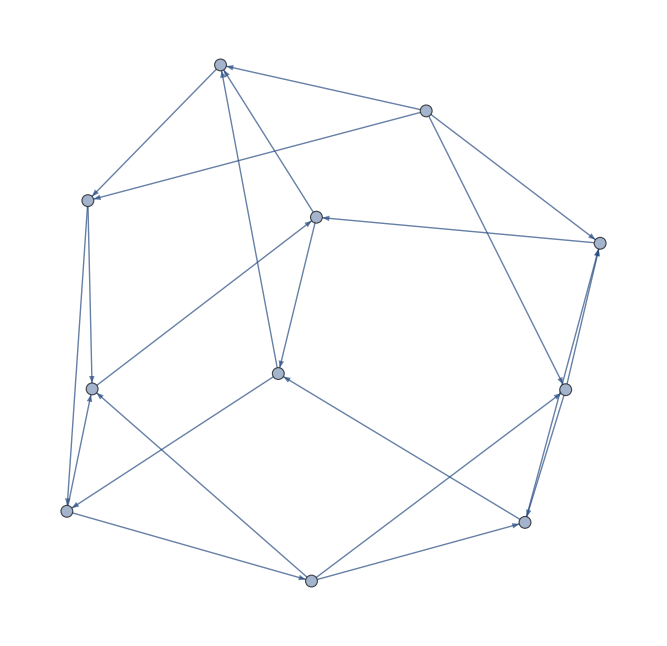
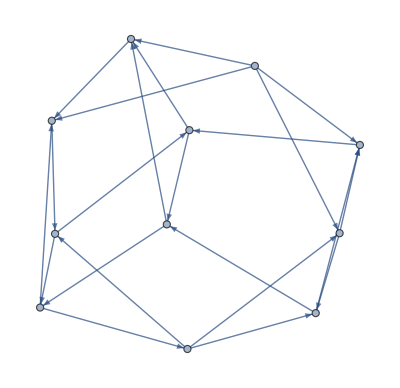
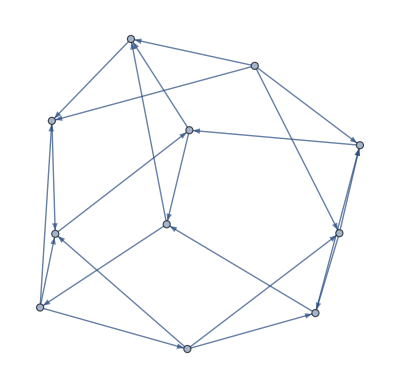
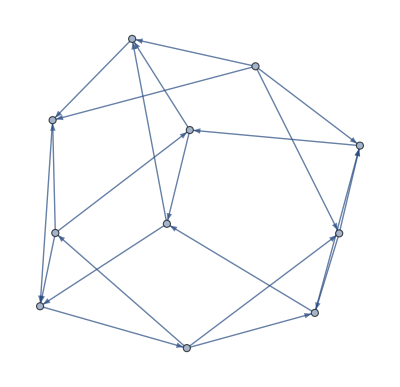
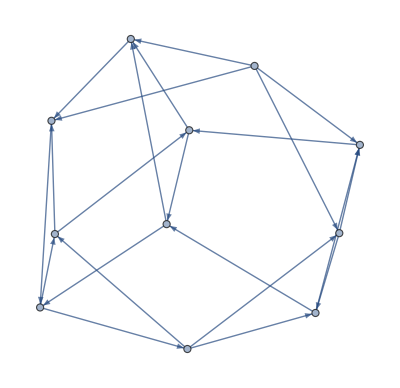
```mathematica
{Length[FindCycle[-Graphics-,∞,All]],-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{21,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Timing[Monitor[Table[Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,comb[g2l,PadLeft[IntegerDigits[n,2],22]]]],∞,All]],{n,2541456,2541456}],n]]
```

{0.002034,{106}}

```mathematica
Timing[Monitor[Table[Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,comb[g2l,PadLeft[IntegerDigits[n,2],22]]]],∞,All]],{n,3000001,3500000}],n]]
Max[%[[2]]]
```

{189.307,{22,18,20,7,18,5,10,5,10,14,18,5,14,8,16,14,16,12,8,6,12,3,3,3,3,4,3,3,4,3,3,2,7,8,12,2,8,2,7,2,7,12,16,2,12,6,15,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,20,20,19,14,14,19,8,8,8,8,11,10,10,11,8,8,23,18,18,8,16,18,7,4,7,4,8,4,10,8,7,4,15,15,16,13,13,16,9,9,9,9,14,12,12,14,12,12,16,12,14,7,14,14,8,5,8,5,10,5,12,10,10,6,499747,29,15,29,9,14,21,29,26,30,14,26,13,21,33,31,24,13,15,24,5,5,15,15,13,9,9,13,6,6,22,18,19,10,18,19,10,6,20,14,20,10,21,18,16,9,38,27,26,10,35,32,14,6,31,19,26,10,35,27,21,9,29,25,28,19,27,28,17,13,34,28,39,27,41,39,37,29,38,27,29,13,37,33,18,9,38,23,37,16,45,34,34,17,14,14,11,6,6,11,2,2,8,8,7,4,4,7,2,2,20,17,14,6,9,14,2,2,10,9,8,4,5,8,2,2,17}}
 |  |  |  |

87

```mathematica
Timing[Monitor[Table[Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,comb[g2l,PadLeft[IntegerDigits[n,2],22]]]],∞,All]],{n,3500001,4000000}],n]]
Max[%[[2]]]
```

{192.998,{19,16,13,9,16,5,7,14,18,16,17,10,18,9,14,19,17,14,7,9,14,3,3,12,11,10,6,7,10,4,4,6,6,9,7,7,9,9,9,3,3,6,4,4,6,6,6,14,9,13,6,13,12,10,7,4,3,6,3,6,6,6,4,7,7,12,10,8,12,12,14,5,5,12,9,7,12,13,15,12,9,12,7,12,12,10,8,6,5,9,5,9,9,10,7,9,13,12,12,6,12,7,9,3,4,6,6,3,6,4,6,15,15,13,9,9,13,6,6,3,3,4,3,3,4,3,3,9,13,15,16,7,15,10,15,5,7,12,13,499722,6,7,0,0,3,1,1,3,3,3,4,4,13,8,8,13,16,16,1,1,12,6,6,12,16,16,10,6,15,6,15,14,18,12,2,1,9,2,9,10,14,9,1,1,10,6,4,10,12,14,0,0,12,7,4,12,15,18,1,1,6,2,4,6,8,6,0,0,6,1,4,6,9,6,6,9,14,14,6,14,12,17,1,2,10,9,2,9,9,14,10,10,12,9,9,12,10,10,1,1,4,2,2,4,4,4,1,2,10,9,2,9,9,14,0,1,11,10,1,10,10,17,1,1,4,2,2,4,4,4,0,0,3,1,1,3,3,3,4}}
 |  |  |  |

87

```mathematica
Timing[Monitor[Table[Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,comb[g2l,PadLeft[IntegerDigits[n,2],22]]]],∞,All]],{n,4000001,4194304}],n]]
Max[%[[2]]]
```

{71.5088,{4,10,6,7,10,12,11,0,0,6,2,3,6,8,7,14,8,17,7,17,15,18,12,1,0,6,1,6,7,9,6,4,4,13,8,8,13,16,16,1,1,12,6,6,12,16,16,9,6,14,6,14,14,17,12,2,1,9,2,9,10,14,9,6,9,10,10,6,12,9,12,0,0,4,2,1,4,4,5,14,12,15,10,12,14,12,11,0,0,3,1,1,3,3,3,6,10,14,15,6,15,12,18,1,2,10,9,2,9,9,14,10,10,12,9,9,12,10,10,1,1,4,2,2,4,4,4,2,2,10,4,7,10,14,11,0,0,9,2,6,9,14,10,9,4,15,4,17,15,194006,1,4,2,4,4,4,4,2,2,4,1,1,1,1,2,1,1,2,1,1,0,0,1,0,0,1,0,0,0,0,2,0,1,2,2,1,4,1,4,0,5,4,2,0,2,0,4,0,5,4,4,1,0,0,1,0,0,1,0,0,0,0,4,1,2,4,5,4,1,0,2,0,2,2,1,0,1,0,4,0,4,4,5,2,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,2,1,2,0,1,2,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0,2,1,0,2,1,2,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,0}}
 |  |  |  |

38

```mathematica
Timing[Monitor[Table[Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,comb[g2l,PadLeft[IntegerDigits[n,2],22]]]],∞,All]],{n,1000001,2000000}],n]]
Max[%[[2]]]
```

{459.617,{21,19,10,18,21,7,7,7,7,9,8,8,9,7,7,23,15,13,2,13,15,1,0,1,0,2,0,2,2,1,0,19,18,18,15,16,19,11,12,11,12,15,15,13,16,13,15,9,6,6,1,6,7,1,0,1,0,2,0,2,2,1,0,22,11,18,6,23,18,12,6,12,6,15,7,20,16,16,10,20,7,15,1,21,15,8,1,8,1,10,1,16,10,10,2,9,5,10,5,13,10,9,5,9,5,13,7,19,18,18,15,4,0,5,0,8,5,4,0,4,0,6,0,9,6,6,1,20,16,16,10,15,17,8,8,8,8,11,10,10,12,999718,11,13,4,3,12,10,10,6,10,11,6,5,3,6,5,5,1,5,1,2,2,4,4,4,1,4,1,2,6,8,7,6,2,6,1,2,2,4,4,4,1,4,1,2,3,7,6,7,1,6,1,3,2,6,6,8,1,7,2,6,3,6,5,5,1,5,1,2,2,4,4,4,1,4,1,2,7,15,10,11,1,10,1,3,3,7,6,7,1,6,1,3,10,16,11,10,2,10,1,2,3,6,5,5,1,5,1,2,6,16,12,16,1,12,1,6,3,12,10,16,1,12,2,10,6,12,8,8,1,8,1,2,3,6,5,5,1,5,1,2,6}}
 |  |  |  |

106

```mathematica
Timing[Monitor[Table[Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,comb[g2l,PadLeft[IntegerDigits[n,2],22]]]],∞,All]],{n,2541456,2541456}],n]]
```

{0.002113,{106}}

```mathematica
Timing[Monitor[Table[Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,comb[g2l,PadLeft[IntegerDigits[n,2],22]]]],∞,All]],{n,1652847,1652847}],n]]
```

{0.001647,{106}}

```mathematica
Position[Out[10],106]
```

{{2,652847}}

```mathematica
Position[Out[31],106]
```

{{2,541456}}

```mathematica
{1,1000000}87
{1000001,2000000}106
```

```mathematica
Max[Out[86]]
```

```mathematica
Flatten[Position[Out[86],Max[Out[86]]]]
```

```mathematica
FromDigits[Map[ToExpression,Characters["0010011001100110011110"]],2]
FromDigits[Map[ToExpression,Characters["0101100110011001100001"]],2]
```

629150

1468001

```mathematica
[[0,1],[0,2],[0,3],[0,4],[1,2],[1,3],[1,5],[2,4],[2,6],[3,7],[3,8],[4,9],[4,10],[5,6],[5,7],[5,9],[6,7],[6,10],[7,8],[8,9],[8,10],[9,10]]
[[0,1],[0,2],[3,0],[0,4],[1,2],[3,1],[5,1],[2,4],[2,6],[7,3],[8,3],[4,9],[4,10],[6,5],[7,5],[5,9],[6,7],[10,6],[8,7],[9,8],[10,8],[9,10]]
{     0,          0,           1,           0,           0,           1,          1,           0,           0,           1,          1,            0,           0,           1,            1,           0,           0,           1,            1,           1,            1,            0}
```

```mathematica
StringReplace["[[0,1],[0,2],[3,0],[0,4],[1,2],[3,1],[5,1],[2,4],[2,6],[7,3],[8,3],[4,9],[4,10],[6,5],[7,5],[5,9],[6,7],[10,6],[8,7],[9,8],[10,8],[9,10]]",{"["->"{","]"->"}"}]
```

```mathematica
StringReplace["{{0,1},{0,2},{3,0},{0,4},{1,2},{3,1},{5,1},{2,4},{2,6},{7,3},{8,3},{4,9},{4,10},{6,5},{7,5},{5,9},{6,7},{10,6},{8,7},{9,8},{10,8},{9,10}}",{","->"->"}]
```

```mathematica
StringReplace["{{0->1}->{0->2}->{3->0}->{0->4}->{1->2}->{3->1}->{5->1}->{2->4}->{2->6}->{7->3}->{8->3}->{4->9}->{4->10}->{6->5}->{7->5}->{5->9}->{6->7}->{10->6}->{8->7}->{9->8}->{10->8}->{9->10}}",{"}->{"->","}]
```

```mathematica
Graph[{0->1,0->2,3->0,0->4,1->2,3->1,5->1,2->4,2->6,7->3,8->3,4->9,4->10,6->5,7->5,5->9,6->7,10->6,8->7,9->8,10->8,9->10}]
```

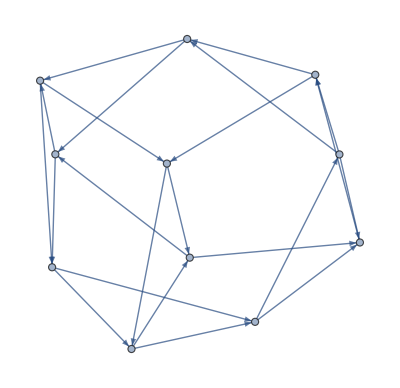
```mathematica
Length[FindCycle[-Graphics-,∞,All]]
```

78

```mathematica
Length[FindCycle[UndirectedGraph[-Graphics-],∞,All]]
```

877

```mathematica
Export["fcylist.py",StringJoin["def cylistf():\n    return ",StringReplace[ToString[Map[{#[[1]],#[[2]]}&,FindCycle[UndirectedGraph[-Graphics-],∞,All],{2}]],{"{"->"[","}"->"]"}]],"TEXT"]
```

fcylist.py

```mathematica
{{{{8<->9,9<->10,10<->8},{5<->6,6<->7,7<->5},{4<->9,9<->10,10<->4},{0<->1,1<->3,3<->0},{3<->7,7<->8,8<->3},{2<->1,1<->0,0<->2},{0<->2,2<->4,4<->0},{5<->6,6<->10,10<->9,9<->5},{7<->5,5<->9,9<->8,8<->7},{7<->6,6<->10,10<->8,8<->7},{4<->9,9<->8,8<->10,10<->4},855,{0<->2,2<->1,1<->5,5<->6,6<->7,7<->3,3<->8,8<->10,10<->9,9<->4,4<->0},{0<->2,2<->1,1<->5,5<->9,9<->8,8<->3,3<->7,7<->6,6<->10,10<->4,4<->0},{0<->1,1<->3,3<->7,7<->5,5<->9,9<->8,8<->10,10<->6,6<->2,2<->4,4<->0},{0<->1,1<->3,3<->7,7<->8,8<->10,10<->9,9<->5,5<->6,6<->2,2<->4,4<->0},{0<->1,1<->3,3<->8,8<->7,7<->5,5<->9,9<->10,10<->6,6<->2,2<->4,4<->0},{0<->1,1<->3,3<->8,8<->10,10<->9,9<->5,5<->7,7<->6,6<->2,2<->4,4<->0},{0<->1,1<->2,2<->6,6<->5,5<->7,7<->3,3<->8,8<->9,9<->10,10<->4,4<->0},{0<->1,1<->2,2<->6,6<->5,5<->7,7<->3,3<->8,8<->10,10<->9,9<->4,4<->0},{0<->1,1<->2,2<->6,6<->10,10<->8,8<->3,3<->7,7<->5,5<->9,9<->4,4<->0},{0<->1,1<->5,5<->7,7<->3,3<->8,8<->9,9<->10,10<->6,6<->2,2<->4,4<->0},{0<->1,1<->5,5<->9,9<->10,10<->8,8<->3,3<->7,7<->6,6<->2,2<->4,4<->0}}}, {{{, , , , }}}}
```

```mathematica
Length[FindCycle[CompleteGraph[4],∞,All]]
```

7

```mathematica
StringReplace["[[0,1],[2,0],[0,3],[4,0],[2,1],[1,3],[1,5],[4,2],[6,2],[3,7],[3,8],[9,4],[10,4],[5,6],[5,7],[9,5],[7,6],[6,10],[7,8],[8,9],[8,10],[10,9]]",{"["->"{","]"->"}"}]
```

```mathematica
Map[Sort,{{0,1},{2,0},{0,3},{4,0},{2,1},{1,3},{1,5},{4,2},{6,2},{3,7},{3,8},{9,4},{10,4},{5,6},{5,7},{9,5},{7,6},{6,10},{7,8},{8,9},{8,10},{10,9}}]
```

```mathematica
StringReplace["{{0,1},{0,2},{0,3},{0,4},{1,2},{1,3},{1,5},{2,4},{2,6},{3,7},{3,8},{4,9},{4,10},{5,6},{5,7},{5,9},{6,7},{6,10},{7,8},{8,9},{8,10},{9,10}}",{"{"->"[","}"->"]"}]
```

```mathematica
Map[#[[1]]->#[[2]]&,{{0,1},{2,0},{0,3},{4,0},{2,1},{1,3},{1,5},{4,2},{6,2},{3,7},{3,8},{9,4},{10,4},{5,6},{5,7},{9,5},{7,6},{6,10},{7,8},{8,9},{8,10},{10,9}}]
```

```mathematica
Length[FindCycle[Graph[{0->1,2->0,0->3,4->0,2->1,1->3,1->5,4->2,6->2,3->7,3->8,9->4,10->4,5->6,5->7,9->5,7->6,6->10,7->8,8->9,8->10,10->9}],∞,All]]
```

105

```mathematica
gl0={{0,1},{0,2},{0,3},{1,2},{1,3},{2,3}};
cgl0[n_]:=Length[FindCycle[Graph[Map[#[[1]]->#[[2]]&,Table[Piecewise[{{gl0[[i]], PadLeft[IntegerDigits[n,2],6][[i]]==0}, {Reverse[gl0[[i]]], PadLeft[IntegerDigits[n,2],6][[i]]==1}}],{i,1,6}]]],∞,All]]
```

```mathematica
Flatten[Position[Table[cgl0[j],{j,0,2^6-1}],3]]-1
```

```mathematica
Column[Select[Map[PadLeft[IntegerDigits[#,2],6]&,{8,10,12,13,17,18,19,21,24,25,26,29,34,37,38,39,42,44,45,46,50,51,53,55}],First[#]==0&]]
```

{0,0,1,0,0,0}
{0,0,1,0,1,0}
{0,0,1,1,0,0}
{0,0,1,1,0,1}
{0,1,0,0,0,1}
{0,1,0,0,1,0}
{0,1,0,0,1,1}
{0,1,0,1,0,1}
{0,1,1,0,0,0}
{0,1,1,0,0,1}
{0,1,1,0,1,0}
{0,1,1,1,0,1}

```mathematica
{0,0,1,0,0,1,0,0,3,1,3,0,3,3,1,0,1,3,3,3,0,3,0,1,3,3,3,1,1,3,0,0,0,0,3,1,1,3,3,3,1,0,3,0,3,3,3,1,0,1,3,3,0,3,1,3,0,0,1,0,0,1,0,0}
```

```mathematica
IntegerDigits[2^6-1,2]
```

{1,1,1,1,1,1}

```mathematica
{{0,1},{0,2},{0,3},{1,2},{1,3},{2,3}}
StringJoin[Reverse[Characters["010101"]]]
```

```mathematica
{{1,0},{0,2},{3,0},{1,2},{3,1},{2,3}}
```

101010

```mathematica
Map[#[[1]]->#[[2]]&,{{1,0},{0,2},{3,0},{1,2},{3,1},{2,3}}]
```

```mathematica
FindCycle[Graph[Map[#[[1]]->#[[2]]&,{{0,1},{0,2},{3,0},{2,1},{1,3},{2,3}}]],∞,All]
```

{{0->2,2->3,3->0},{0->1,1->3,3->0},{0->2,2->1,1->3,3->0}}

```mathematica
FindCycle[Graph[{0->1,2->0,0->3,2->1,1->3,3->2}],∞,All]
```

{{1->3,3->2,2->1},{0->3,3->2,2->0},{0->1,1->3,3->2,2->0}}

```mathematica
HamiltonianGraphQ[CompleteGraph[4]]
```

True

```mathematica
Length[FindCycle[CompleteGraph[4],∞,All]]
```

7

```mathematica
FromDigits[IntegerDigits[010101],2]
```

21

```mathematica
Graph[Map[#[[1]]->#[[2]]&,{{0,1},
{1,2},
{2,0},
{2,3},
{3,0},
{1,3}}]]
```

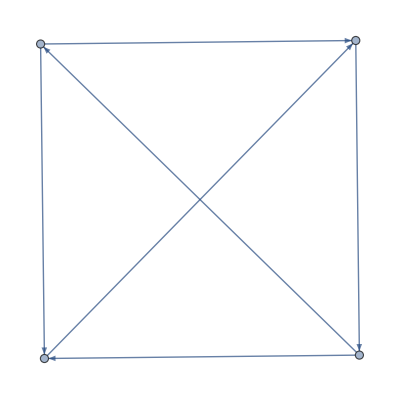
```mathematica
Length[FindCycle[-Graphics-,∞,All]]
```

3